```mathematica
ClearAll["`*"]
f[s_]=-20 s^7+70 s^6-84 s^5+35 s^4
arg[t_,ϵ_] := 1/2*(1/ϵ t+1)
```

35 s^4-84 s^5+70 s^6-20 s^7

```mathematica
g[t_, ϵ_]=f[arg[t,ϵ]]//FullSimplify//ExpandAll
g1[t_, ϵ_]=D[f[arg[t,ϵ]],t]//FullSimplify//ExpandAll
g2[t_, ϵ_]=D[f[arg[t,ϵ]],{t,2}]//FullSimplify//ExpandAll
```

1/2-(5 t^7)/(32 ϵ^7)+(21 t^5)/(32 ϵ^5)-(35 t^3)/(32 ϵ^3)+(35 t)/(32 ϵ)

-(35 t^6)/(32 ϵ^7)+(105 t^4)/(32 ϵ^5)-(105 t^2)/(32 ϵ^3)+35/(32 ϵ)

-(105 t^5)/(16 ϵ^7)+(105 t^3)/(8 ϵ^5)-(105 t)/(16 ϵ^3)

```mathematica
D[g[t,ϵ],t]==g1[t,ϵ]
D[g[t,ϵ],{t,2}]==g2[t,ϵ]
```

True

True

```mathematica
k
```

1/2-(5 t^7)/(32 ϵ^7)+(21 t^5)/(32 ϵ^5)-(35 t^3)/(32 ϵ^3)+(35 t)/(32 ϵ)

-(35 t^6)/(32 ϵ^7)+(105 t^4)/(32 ϵ^5)-(105 t^2)/(32 ϵ^3)+35/(32 ϵ)

-(105 t^5)/(16 ϵ^7)+(105 t^3)/(8 ϵ^5)-(105 t)/(16 ϵ^3)

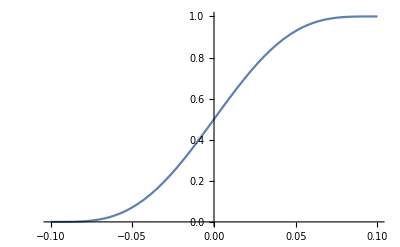

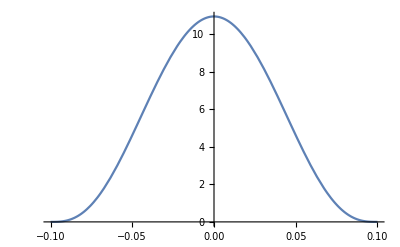

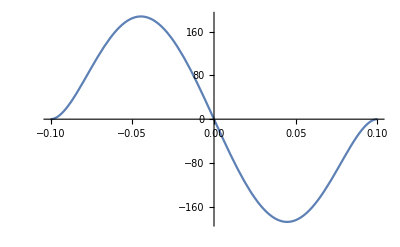

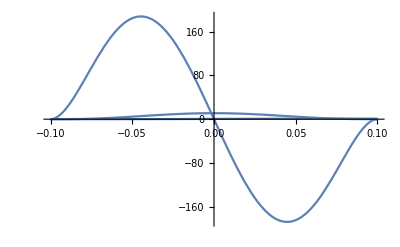

```mathematica
g[t,ϵ]
g1[t,ϵ]
g2[t,ϵ]

ϵ0 := .1;
p=Plot[g[t, ϵ0], {t,-ϵ0, ϵ0}]
p1=Plot[g1[t, ϵ0], {t,-ϵ0, ϵ0}]
p2=Plot[g2[t, ϵ0], {t,-ϵ0, ϵ0}]
Show[{p,p1,p2},PlotRange->Automatic]
```